# Richard the Trebuchet

Charlie Bushman, Axel Stahl, Kyle Fraser-Mines, Jack Heinzel
Phys 231
Start: 03-09-19
Finish: 03-18-19

This notebook performs a computational analysis of the dynamics of a trebuchet as certain initial system parameters are varied. Section 0 will set up the simulation of the trebuchet, using a Lagrange multiplier to keep the projectile on a tread until it lifts off and then acts without the multiplier. Section 1 will investigate the effect of the fulcrum offset on the range of the trebuchet and Section 2 will investigate the effect of the sling length on the range of the trebuchet. Section 3 will make a comparison between the range of the trebuchet on wheels and the range without wheels to see which can launch further. Finally, Section 4 will investigate the effect of the initial position of the counterweight on the trebuchet’s range.

## Section 0 : How Does He Do It?

In this section we will be using Lagrangian methods to simulate the motion of a trebuchet that has a hanging counterweight (free to rotate), a sling, and wheels. This will allow four degrees of freedom in the model: with all angles being measured from the horizontal, the angle of the throwing arm, the angle of the sling, the angle of the counterweight, and the position of the center of the body. The module simulateTreb1[] will simulate the trebuchet with the additional constraint that the projectile remains on a tread. The module simulateTreb2[] will simulate the trebuchet without that constraint. Finally, the module simulateTreb[] will combine the two, by taking the results of simulateTreb1[] until the Lagrange multiplier equals 0 and then switching to the results of simulateTreb2[].

Throughout the notebook, list1 and list2 are two common variables in use. These are lists of initial values for the trebuchet which are ordered thusly:
The order for list1 should be: r[0],θ[0],ϕ[0],σ[0],r’[0],θ’[0],ϕ’[0],σ’[0]
The order for list2 should be: h,d,l1,l2,l3,l,m1,m2,m3,m4,g

```mathematica
Clear[list1,list2,rt,θt,ϕt,σt,λt,rt1,θt1,ϕt1,σt1,rt2,θt2,ϕt2,σt2,plotr,plotθ,plotϕ,plotσ,plotλ,animation,r,θ,ϕ,σ]
simulateTreb1[list1_,list2_,tf_:1]:=Module[{x1,x2,x3,h1,h2,h3,λ,T,U,L,r,θ,ϕ,σ,h=list2[[1]],d=list2[[2]],l1=list2[[3]],l2=list2[[4]],l3=list2[[5]],l=list2[[6]],m1=list2[[7]],m2=list2[[8]],m3=list2[[9]],m4=list2[[10]],g=list2[[11]]},
(*Equations of kinetic energy*)
(*Note the 'var' followed by a 'g' (for generalized) is to avoid scoping complications with the same variable names used in the module*)
x1[rg_,ϕg_,θg_]= rg+l2 Cos[ϕg]-(l/2+d)Cos[θg];
x2[rg_,θg_]=rg-d Cos[θg];
x3[rg_,θg_,σg_]=rg+(l/2-d)Cos[θg]+l3 Cos[σg];
h1[θg_,ϕg_]=h-(l1/2+d)Sin[θg]-l2 Sin[ϕg];
h2[θg_]=h-d Sin[θg];
h3[θg_,σg_]=h+(l1/2-d)Sin[θg]-l3 Sin[σg];
(*Set up the constraint function*)
gFxn=h-(l1/2+d)Sin[θ[t]]-l2 Sin[ϕ[t]];
(*Full kinetic energy term in terms of generalized coordinates*)
T=m1/2(D[h1[θ[t],ϕ[t]],t]^2+D[x1[r[t],ϕ[t],θ[t]],t]^2)+m2/2(D[h2[θ[t]],t]^2+D[x2[r[t],θ[t]],t]^2)+m3/2(D[h3[θ[t],σ[t]],t]^2+D[x3[r[t],θ[t],σ[t]],t]^2)+m2 D[θ[t],t]^2(l1^2)/24+m4/2(D[r[t],t])^2;
(*Potential term in terms of generalized coordinates*)
U=m3 g h3[θ[t],σ[t]]+m1 g h1[θ[t],ϕ[t]]+m2 g h2[θ[t]];
(*Setting up the Lagrangian and the Euler-Lagrange equations*)
L:=T-U;
Clear[EL];
EL[q_]:=D[D[L,q'[t]],t]-D[L,q[t]]+λ[t]*D[gFxn,q[t]]==0;
(*Numerical solution*)
soln = NDSolve[{
EL[r],
EL[θ],
EL[ϕ],
EL[σ],
r[0] == list1[[1]],
θ[0]==list1[[2]],
ϕ[0]==list1[[3]],
σ[0]==list1[[4]],
r'[0] == list1[[5]],
θ'[0]==list1[[6]],
ϕ'[0]==list1[[7]],
σ'[0]==list1[[8]],
D[gFxn,t,t]==0},{r[t],θ[t],ϕ[t],σ[t],λ[t]},{t,0,tf}];
(*Pull off the solutions. These are left as external variables so that they can be
accessed by later modules.*)
rt1[t_]=soln[[1,1,2]];
θt1[t_]=soln[[1,2,2]];
ϕt1[t_]=soln[[1,3,2]];
σt1[t_]=soln[[1,4,2]];
(*Figure out the time at which the projectile leaves the tread*)
λt[t_]=soln[[1,5,2]];
]
(*This module simulates the trebuchet after the projectile has left the track*)
simulateTreb2[list1_,list2_,tf_:1]:=Module[{x1,x2,x3,h1,h2,h3,T,U,L,r,θ,ϕ,σ,h=list2[[1]],d=list2[[2]],l1=list2[[3]],l2=list2[[4]],l3=list2[[5]],l=list2[[6]],m1=list2[[7]],m2=list2[[8]],m3=list2[[9]],m4=list2[[10]],g=list2[[11]]},
(*Equations of kinetic energy*)
(*Note the 'var' followed by a 'g' (for generalized) is to avoid scoping complications with the same variable names used in the module*)
x1[rg_,ϕg_,θg_]= rg+l2 Cos[ϕg]-(l/2+d)Cos[θg];
x2[rg_,θg_]=rg-d Cos[θg];
x3[rg_,θg_,σg_]=rg+(l/2-d)Cos[θg]+l3 Cos[σg];
h1[θg_,ϕg_]=h-(l1/2+d)Sin[θg]-l2 Sin[ϕg];
h2[θg_]=h-d Sin[θg];
h3[θg_,σg_]=h+(l1/2-d)Sin[θg]-l3 Sin[σg];
(*Full kinetic energy term in terms of generalized coordinates*)
T=m1/2(D[h1[θ[t],ϕ[t]],t]^2+D[x1[r[t],ϕ[t],θ[t]],t]^2)+m2/2(D[h2[θ[t]],t]^2+D[x2[r[t],θ[t]],t]^2)+m3/2(D[h3[θ[t],σ[t]],t]^2+D[x3[r[t],θ[t],σ[t]],t]^2)+m2 D[θ[t],t]^2(l1^2)/24+m4/2(D[r[t],t])^2;
(*Potential term in terms of generalized coordinates*)
U=m3 g h3[θ[t],σ[t]]+m1 g h1[θ[t],ϕ[t]]+m2 g h2[θ[t]];
(*Setting up the Lagrangian and the Euler-Lagrange equations*)
L:=T-U;
Clear[EL];
EL[q_]:=D[D[L,q'[t]],t]-D[L,q[t]]==0;
(*Numerical solution*)
soln = NDSolve[{
EL[r],
EL[θ],
EL[ϕ],
EL[σ],
r[0] == list1[[1]],
θ[0]==list1[[2]],
ϕ[0]==list1[[3]],
σ[0]==list1[[4]],
r'[0] == list1[[5]],
θ'[0]==list1[[6]],
ϕ'[0]==list1[[7]],
σ'[0]==list1[[8]]},{r[t],θ[t],ϕ[t],σ[t]},{t,0,tf}];
(*Pull off the solutions. These are left as external variables so that they can be
accessed by later modules.*)
rt2[t_]=soln[[1,1,2]];
θt2[t_]=soln[[1,2,2]];
ϕt2[t_]=soln[[1,3,2]];
σt2[t_]=soln[[1,4,2]];
]
```

One interesting thing to note about this simulation is that, for certain initial conditions, the simulation does not work well at all. For example, with an initial counterweight angle (σ[0]) of -π/19, the simulation is completely unrealistic.

```mathematica
(*The order for list1 should be: r[0],θ[0],ϕ[0],σ[0],r'[0],θ'[0],ϕ'[0],σ'[0]*)
(*The order for list2 should be: h,d,l1,l2,l3,l,m1,m2,m3,m4,g*)
list1={0,π/5,0,0.7,0,0,0,0};
list2={0.45,0.07,0.74,0.44,0.12,0.74,0.01,0.1,0.15,0.1,9.81};
simulateTreb1[list1,list2];
(*Set value for initial time and generalized coordinates at this time*)
t0=FindRoot[λt[t],{t,0.25}][[All,2]][[1]];
newList1={rt1[t0],θt1[t0],ϕt1[t0],σt1[t0],rt1'[t0],θt1'[t0],ϕt1'[t0],σt1'[t0]};
simulateTreb2[newList1,list2];
(*Combine the results of the two simulation modules*)
rt[t_]=Piecewise[{{rt1[t],t<t0},{rt2[t-t0],t>t0}}];
θt[t_]=Piecewise[{{θt1[t],t<t0},{θt2[t-t0],t>t0}}];
ϕt[t_]=Piecewise[{{ϕt1[t],t<t0},{ϕt2[t-t0],t>t0}}];
σt[t_]=Piecewise[{{σt1[t],t<t0},{σt2[t-t0],t>t0}}];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

```mathematica
plotTreb[rt_,θt_,ϕt_,σt_,λt_]:=Module[{s},
plotr=Plot[rt[s],{s,0,1},Frame->True,FrameLabel->{"t","r","r[t]",""},Axes->None,ImageSize->Medium,GridLines->Automatic];
plotθ=Plot[θt[s],{s,0,1},Frame->True,FrameLabel->{"t","θ","θ[t]",""},Axes->None,ImageSize->Medium,GridLines->Automatic];
plotϕ=Plot[ϕt[s],{s,0,1},Frame->True,FrameLabel->{"t","ϕ","ϕ[t]",""},Axes->None,ImageSize->Medium,GridLines->Automatic];
plotσ=Plot[σt[s],{s,0,1},Frame->True,FrameLabel->{"t","σ","σ[t]",""},Axes->None,ImageSize->Medium,GridLines->Automatic];
plotλ=Plot[λt[s],{s,0,1},Frame->True,FrameLabel->{"t","λ","λ[t]",""},Axes->None,ImageSize->Medium,GridLines->Automatic];
]
```

These plots show the generalized coordinates as functions of time using the piecewise functions constructed above. In the simulateTreb[] module, the piecewise graphs are converted to singular interpolating functions without any apparent loss of information.

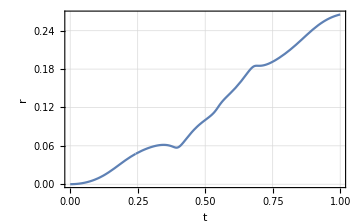

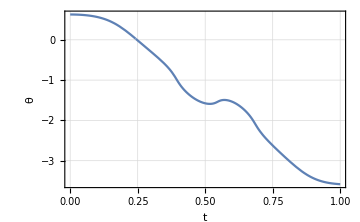

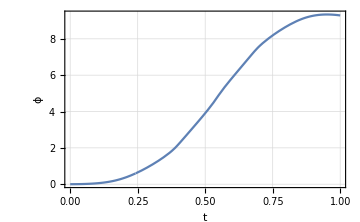

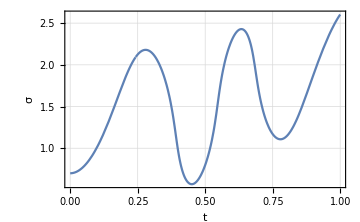

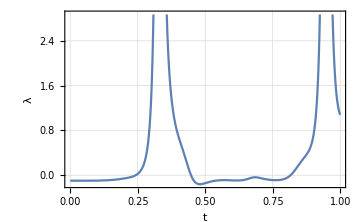

```mathematica
plotTreb[rt,θt,ϕt,σt,λt];
plotr
plotθ
plotϕ
plotσ
plotλ
```

```mathematica
animateTreb[rt_,θt_,ϕt_,σt_,list2_]:=Module[{h=list2[[1]],d=list2[[2]],l1=list2[[3]],l2=list2[[4]],l3=list2[[5]],l=list2[[6]],m1=list2[[7]],m2=list2[[8]],m3=list2[[9]],m4=list2[[10]],g=list2[[11]]},
animation=Manipulate[Graphics[{
Blue,Line[{{-1,0},{1,0}}],
Blue,Line[{{-1,-.5},{-1,1.5}}],
Red,Rectangle[{rt[s]-.2,0},{rt[s]+0.4,0.1}],
Black,Line[{{rt[s]+0.1,0.1},{rt[s]+0.1,h}}],
Black,Line[{{rt[s]+0.1+(l/2-d)Cos[θt[s]],h+(l/2-d)Sin[θt[s]]},{rt[s]+0.1-(l/2+d)Cos[θt[s]],h-(l/2+d)Sin[θt[s]]}}],
Red,Line[{{rt[s]+0.1-(l/2+d)Cos[θt[s]],h-(l/2+d)Sin[θt[s]]},{rt[s]+0.1-(l/2+d)Cos[θt[s]]+l2 Cos[ϕt[s]],h-(l/2+d)Sin[θt[s]]-l2 Sin[ϕt[s]]}}],
Green,Circle[{rt[s]+0.1-(l/2+d)Cos[θt[s]]+l2 Cos[ϕt[s]],h-(l/2+d)Sin[θt[s]]-l2 Sin[ϕt[s]]},0.05],
Red, Line[{{rt[s]+0.1+(l/2-d)Cos[θt[s]],h+(l/2-d)Sin[θt[s]]},{rt[s]+0.1+(l/2-d)Cos[θt[s]]+l3 Cos[σt[s]],h+(l/2-d)Sin[θt[s]]-l3 Sin[σt[s]]}}],
Green, Circle[{rt[s]+0.1+(l/2-d)Cos[θt[s]]+l3 Cos[σt[s]],h+(l/2-d)Sin[θt[s]]-l3 Sin[σt[s]]},0.1]
}],{s,0,1}]
]
```

```mathematica
list2={0.45,0.06,1.125,0.44,0.12,1.125,0.01,0.1,0.3,0.1,9.81}
list1={0,π/5,0,Pi/2,0,0,0,0}
simulateTreb[list1,list2]
animateTreb[rt,θt,ϕt,σt,list2];
animation
```

{0.45,0.06,1.125,0.44,0.12,1.125,0.01,0.1,0.3,0.1,9.81}

{0,π/5,0,π/2,0,0,0,0}

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

These equations are used to find the time at which the trebuchet will release the projectile. Instead of assuming an optimal launch angle of π/4, this solves for the time at which θ[t] is equal to ϕ[t] (when the arm is in line with the sling) because that is when our projectile releases in the physical model according to our slow motion video analysis.

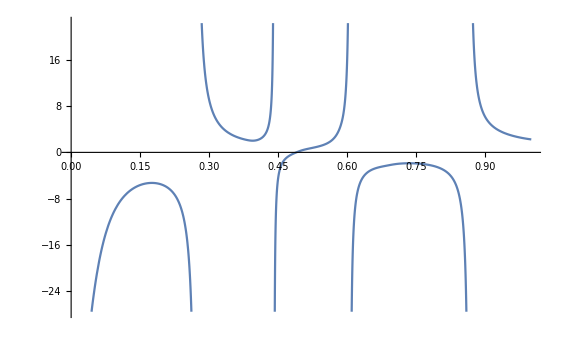

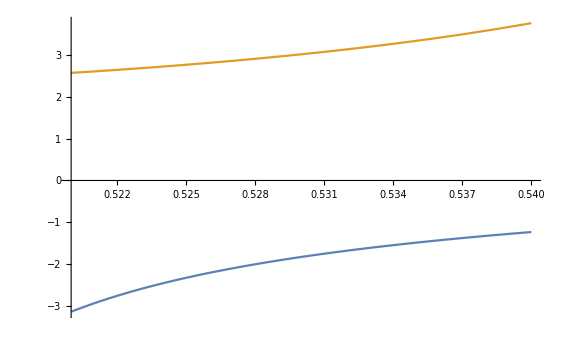

{t→0.48939}

```mathematica
eq[t_]=Piecewise[{{Tan[ϕt[t]+Pi/2]+Tan[θt[t]+Pi/2],0<t<1},{Indeterminate,t>1}, {Indeterminate,t<0}}];
Plot[{eq[t]},{t,0,1}]
Plot[{Tan[ϕt[t]],-Tan[θt[t]]},{t,.52,.54}]
FindRoot[eq[t],{t,0.5}]
```

```mathematica
simulateTreb[list1_,list2_]:=Module[{t0,tf=1,newList1},
simulateTreb1[list1,list2,tf];
(*Set value for initial time and generalized coordinates at this time*)
t0=FindRoot[λt[t],{t,0.25}][[All,2]][[1]];
newList1={rt1[t0],θt1[t0],ϕt1[t0],σt1[t0],rt1'[t0],θt1'[t0],ϕt1'[t0],σt1'[t0]};
simulateTreb2[newList1,list2,tf];
(*Combine the results of the two simulation modules*)
prt[t_]=Piecewise[{{rt1[t],t<t0},{rt2[t-t0],t>t0}}];
pθt[t_]=Piecewise[{{θt1[t],t<t0},{θt2[t-t0],t>t0}}];
pϕt[t_]=Piecewise[{{ϕt1[t],t<t0},{ϕt2[t-t0],t>t0}}];
pσt[t_]=Piecewise[{{σt1[t],t<t0},{σt2[t-t0],t>t0}}];
rt=Interpolation[Table[{s,prt[s]},{s,0,1,0.001}]];
θt=Interpolation[Table[{s,pθt[s]},{s,0,1,0.001}]];
ϕt=Interpolation[Table[{s,pϕt[s]},{s,0,1,0.001}]];
σt=Interpolation[Table[{s,pσt[s]},{s,0,1,0.001}]];
]
```

## Section 1 : Optimization of Fulcrum Position

This section contains an investigation of the effect of the fulcrum position on the firing range of the trebuchet. This will be achieved by varying the desired initial condition in a loop and outputting the resulting ranges on a graph. The speed is calculated according to the speed[] equation detailed in the loop. The process remains very similar for Sections 2 and 4 as well. The range of values was chosen by trial and error.

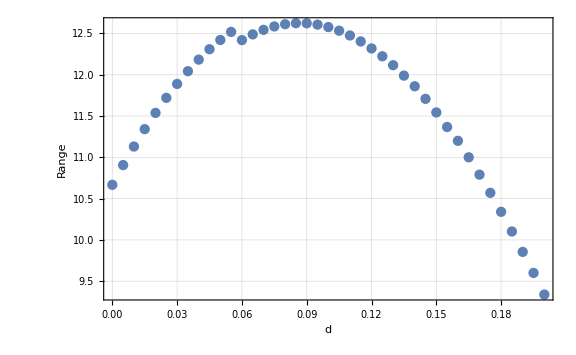

```mathematica
Clear[dvPairs,releaseTime];
releaseTime;
list1={0,π/5,0,π/2,0,0,0,0};
list2={0.45,0.07,1.225,0.4,0.12,1.225,0.008,0.1,0.15,0.1,9.81};
dvPairs=Monitor[Table[list2={0.45,newD,1.125,0.4,0.12,1.125,0.01,0.1,0.3,0.1,9.81};simulateTreb[list1,list2];
xt[rg_,ϕg_,θg_]=rg+list2[[4]] Cos[ϕg]-(list2[[6]]/2+list2[[2]]) Cos[θg];ht[θg_,ϕg_]=list2[[1]]-(list2[[3]]/2+list2[[2]]) Sin[θg]-list2[[4]] Sin[ϕg];speed[t_]=(1/9.81)((D[xt[rt[t],ϕt[t],θt[t]],t])^2+(D[ht[θt[t],ϕt[t]],t])^2)Sin[2(θt[t]+Pi/2)];
eq[t_]=Piecewise[{{Tan[ϕt[t]+Pi/2]+Tan[θt[t]+Pi/2],0<t<1},{Indeterminate,t>1}, {Indeterminate,t<0}}];
releaseTime=FindRoot[eq[t],{t,0.5}][[All,2]][[1]];{newD,speed[releaseTime]},{newD,0,0.2,0.005}],newD]//Quiet;
dvPlot1=ListPlot[dvPairs,Frame->True,FrameLabel->{"d","Range","Release Velocity as a Function of Axle Placement",""},Axes->Automatic,ImageSize->Large,GridLines->Automatic]
```

This graph has a distinctive peak which spans offsets of roughly 0.05 to 0.10 meters. With this wide a peak, it is reasonably easy to optimize this parameter in the real model. One feature of note here is the jagged behavior around d = 0.06 m. It is hard to say what causes this shift between one smooth curve and another, but given that the shift is not very substantial and that it occurs at the edge of the optimal parameter range, it is unlikely to be impactful.

## Section 2 : Release Velocity as a Function of Sling Length

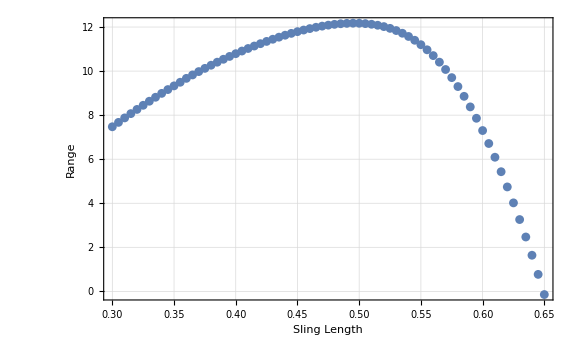

```mathematica
list1={0,π/5,0,π/2,0,0,0,0};
list2={0.45,0.1,0.74,0.44,0.12,0.74,0.01,0.1,0.17,0.1,9.81};
slingvPairs=Monitor[Table[list2={0.45,0.17,1.125,newSling,0.12,1.125,0.01,0.1,0.3,0.1,9.81};simulateTreb[list1,list2];xt[rg_,ϕg_,θg_]=rg+list2[[4]] Cos[ϕg]-(list2[[6]]/2+list2[[2]]) Cos[θg];ht[θg_,ϕg_]=list2[[1]]-(list2[[3]]/2+list2[[2]]) Sin[θg]-list2[[4]] Sin[ϕg];speed[t_]=(1/9.81)((D[xt[rt[t],ϕt[t],θt[t]],t])^2+(D[ht[θt[t],ϕt[t]],t])^2)Sin[2(θt[t]+Pi/2)];
eq[t_]=Piecewise[{{Tan[ϕt[t]+Pi/2]+Tan[θt[t]+Pi/2],0<t<1},{Indeterminate,t>1}, {Indeterminate,t<0}}];
releaseTime=FindRoot[eq[t],{t,0.5}][[All,2]][[1]];{newSling,speed[releaseTime]},{newSling,0.3,0.65,0.005}],newSling]//Quiet;
ListPlot[slingvPairs,Frame->True,FrameLabel->{"Sling Length","Range","Release Velocity as a Function of Sling Length",""},Axes->Automatic,ImageSize->Large,GridLines->Automatic]
```

In this section, we look at how the sling length affects the release velocity of the trebuchet’s projectile. The result of another smooth curve is very nice and nicer still because the peak range occurs over a wide range of sling lengths, roughly 0.45 to 0.55 meters. This is again an easy task to implement in the physical model. It is also clear from this plot that erring on the side of a shorter sling is a good idea as the left hand side of the peak falls off much less quickly than the right hand side.

## Section 2.1 : Combined Effects of Sling Length and Fulcrum Position

In this section, we look at the combined effects of the sling length and the fulcrum position on the range of the trebuchet. The resultant 3-D plot will ensure that both of these parameters are optimized without being at the expense of the other.

```mathematica
list1={0,π/5,0,π/2,0,0,0,0};
list2={0.45,0.12,1.125,0.44,0.12,1.125,0.01,0.1,0.15,0.1,9.81};
slingdvPairs=Monitor[Table[list2={0.45,newD,1.125,newSling,0.12,1.125,0.01,0.1,0.3,0.1,9.81};simulateTreb[list1,list2];xt[rg_,ϕg_,θg_]=rg+list2[[4]] Cos[ϕg]-(list2[[6]]/2+list2[[2]]) Cos[θg];ht[θg_,ϕg_]=list2[[1]]-(list2[[3]]/2+list2[[2]]) Sin[θg]-list2[[4]] Sin[ϕg];speed[t_]=(1/9.81)((D[xt[rt[t],ϕt[t],θt[t]],t])^2+(D[ht[θt[t],ϕt[t]],t])^2)Sin[2(θt[t]+Pi/2)];
eq[t_]=Piecewise[{{Tan[ϕt[t]+Pi/2]+Tan[θt[t]+Pi/2],0<t<1},{Undefined,t>1}, {Undefined,t<0}}];
releaseTime=FindRoot[eq[t],{t,0.5}][[All,2]][[1]];{newD,newSling,speed[releaseTime]},{newD,.05,0.15,0.005},{newSling,0.4,.56,0.005}],{newD,newSling}]//Quiet;
```

```mathematica
slingdvPairs1=Flatten[slingdvPairs,1];
newSlingdvPairs=Table[If[NumberQ[slingdvPairs1[[i,3]]]&& slingdvPairs1[[i,3]]<100&&slingdvPairs1[[i,3]]>3,slingdvPairs1[[i]],0],{i,1,Length[slingdvPairs1]}]//DeleteCases[0];
ListPlot3D[newSlingdvPairs,Mesh->None,InterpolationOrder->1,ColorFunction->"TemperatureMap",AxesLabel->{"Fulcrum Offset","Sling Length","Range"},FaceGrids->All]
```

-Graphics3D-

The peak of the combined plots appears in exactly the position that would have been predicted by the two individually. This means that we can continue with the optimized parameter values determined from Sections 1 and 2.

## Section 3 : Does Richard Need Heelys or Nah?

In this professionally named section we investigate what effect wheels have on the range of the trebuchet. To do this, we create a new Lagrangian model with only three degrees of freedom, excluding the r value, and run the simulation with the optimized parameter set we have found so far.

```mathematica
(*This module simulates the trebuchet from t=0 to when the projectile leaves the tread*)
Clear[list1,list2,rt,θt,ϕt,σt,λt,rt1,θt1,ϕt1,σt1,rt2,θt2,ϕt2,σt2,plotr,plotθ,plotϕ,plotσ,plotλ,animation,r,θ,ϕ,σ]
simulateTrebWheeless1[list1_,list2_,tf_:1]:=Module[{x1,x2,x3,h1,h2,h3,λ,T,U,L,r,θ,ϕ,σ,h=list2[[1]],d=list2[[2]],l1=list2[[3]],l2=list2[[4]],l3=list2[[5]],l=list2[[6]],m1=list2[[7]],m2=list2[[8]],m3=list2[[9]],m4=list2[[10]],g=list2[[11]]},
(*Equations of kinetic energy*)
(*Note the 'var' followed by a 'g' (for generalized) is to avoid scoping complications with the same variable names used in the module*)
x1[ϕg_,θg_]= l2 Cos[ϕg]-(l/2+d)Cos[θg];
x2[θg_]=d Cos[θg];
x3[θg_,σg_]=(l/2-d)Cos[θg]+l3 Cos[σg];
h1[θg_,ϕg_]=h-(l1/2+d)Sin[θg]-l2 Sin[ϕg];
h2[θg_]=h-d Sin[θg];
h3[θg_,σg_]=h+(l1/2-d)Sin[θg]-l3 Sin[σg];
(*Set up the constraint function*)
gFxn=h-(l1/2+d)Sin[θ[t]]-l2 Sin[ϕ[t]];
(*Full kinetic energy term in terms of generalized coordinates*)
T=m1/2(D[h1[θ[t],ϕ[t]],t]^2+D[x1[ϕ[t],θ[t]],t]^2)+m2/2(D[h2[θ[t]],t]^2+D[x2[θ[t]],t]^2)+m3/2(D[h3[θ[t],σ[t]],t]^2+D[x3[θ[t],σ[t]],t]^2)+m2 D[θ[t],t]^2(l1^2)/24;
(*Potential term in terms of generalized coordinates*)
U=m3 g h3[θ[t],σ[t]]+m1 g h1[θ[t],ϕ[t]]+m2 g h2[θ[t]];
(*Setting up the Lagrangian and the Euler-Lagrange equations*)
L:=T-U;
Clear[EL];
EL[q_]:=D[D[L,q'[t]],t]-D[L,q[t]]+λ[t]*D[gFxn,q[t]]==0;
(*Numerical solution*)
soln = NDSolve[{
EL[θ],
EL[ϕ],
EL[σ],
θ[0]==list1[[1]],
ϕ[0]==list1[[2]],
σ[0]==list1[[3]],
θ'[0]==list1[[4]],
ϕ'[0]==list1[[5]],
σ'[0]==list1[[6]],
D[gFxn,t,t]==0},{θ[t],ϕ[t],σ[t],λ[t]},{t,0,tf}];
(*Pull off the solutions. These are left as external variables so that they can be
accessed by later modules.*)
θt1[t_]=soln[[1,1,2]];
ϕt1[t_]=soln[[1,2,2]];
σt1[t_]=soln[[1,3,2]];
(*Figure out the time at which the projectile leaves the tread*)
λt[t_]=soln[[1,4,2]];
]
(*This module simulates the trebuchet after the projectile has left the track*)
simulateTrebWheeless2[list1_,list2_,tf_:1]:=Module[{x1,x2,x3,h1,h2,h3,T,U,L,r,θ,ϕ,σ,h=list2[[1]],d=list2[[2]],l1=list2[[3]],l2=list2[[4]],l3=list2[[5]],l=list2[[6]],m1=list2[[7]],m2=list2[[8]],m3=list2[[9]],m4=list2[[10]],g=list2[[11]]},
(*Equations of kinetic energy*)
(*Note the 'var' followed by a 'g' (for generalized) is to avoid scoping complications with the same variable names used in the module*)
x1[ϕg_,θg_]= l2 Cos[ϕg]-(l/2+d)Cos[θg];
x2[θg_]=d Cos[θg];
x3[θg_,σg_]=(l/2-d)Cos[θg]+l3 Cos[σg];
h1[θg_,ϕg_]=h-(l1/2+d)Sin[θg]-l2 Sin[ϕg];
h2[θg_]=h-d Sin[θg];
h3[θg_,σg_]=h+(l1/2-d)Sin[θg]-l3 Sin[σg];
(*Full kinetic energy term in terms of generalized coordinates*)
T=m1/2(D[h1[θ[t],ϕ[t]],t]^2+D[x1[ϕ[t],θ[t]],t]^2)+m2/2(D[h2[θ[t]],t]^2+D[x2[θ[t]],t]^2)+m3/2(D[h3[θ[t],σ[t]],t]^2+D[x3[θ[t],σ[t]],t]^2)+m2 D[θ[t],t]^2(l1^2)/24;
(*Potential term in terms of generalized coordinates*)
U=m3 g h3[θ[t],σ[t]]+m1 g h1[θ[t],ϕ[t]]+m2 g h2[θ[t]];
(*Setting up the Lagrangian and the Euler-Lagrange equations*)
L:=T-U;
Clear[EL];
EL[q_]:=D[D[L,q'[t]],t]-D[L,q[t]]==0;
(*Numerical solution*)
soln = NDSolve[{
EL[θ],
EL[ϕ],
EL[σ],
θ[0]==list1[[1]],
ϕ[0]==list1[[2]],
σ[0]==list1[[3]],
θ'[0]==list1[[4]],
ϕ'[0]==list1[[5]],
σ'[0]==list1[[6]]},{θ[t],ϕ[t],σ[t]},{t,0,tf}];
(*Pull off the solutions. These are left as external variables so that they can be
accessed by later modules.*)
θt2[t_]=soln[[1,1,2]];
ϕt2[t_]=soln[[1,2,2]];
σt2[t_]=soln[[1,3,2]];
]
```

```mathematica
list1={π/5,0,π/2,0,0,0};
list2={0.45,0.07,0.74,0.44,0.12,0.74,0.01,0.1,0.15,0.1,9.81};
simulateTrebWheeless1[list1,list2];
(*Set value for initial time and generalized coordinates at this time*)
t0=FindRoot[λt[t],{t,0.25}][[All,2]][[1]];
newList1={θt1[t0],ϕt1[t0],σt1[t0],θt1'[t0],ϕt1'[t0],σt1'[t0]};
simulateTrebWheeless2[newList1,list2];
(*Combine the results of the two simulation modules*)
θt[t_]=Piecewise[{{θt1[t],t<t0},{θt2[t-t0],t>t0}}];
ϕt[t_]=Piecewise[{{ϕt1[t],t<t0},{ϕt2[t-t0],t>t0}}];
σt[t_]=Piecewise[{{σt1[t],t<t0},{σt2[t-t0],t>t0}}];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

```mathematica
rt[t_]=0;
animateTreb[rt,θt,ϕt,σt,list2];
animation
```

```mathematica
θt=Interpolation[Table[{s,θt[s]},{s,0,1,0.001}]];
ϕt=Interpolation[Table[{s,ϕt[s]},{s,0,1,0.001}]];
σt=Interpolation[Table[{s,σt[s]},{s,0,1,0.001}]];
xt[rg_,ϕg_,θg_]=rg+list2[[4]] Cos[ϕg]-(list2[[6]]/2+list2[[2]]) Cos[θg];ht[θg_,ϕg_]=list2[[1]]-(list2[[3]]/2+list2[[2]]) Sin[θg]-list2[[4]] Sin[ϕg];speed[t_]=((D[xt[rt[t],ϕt[t],θt[t]],t])^2+(D[ht[θt[t],ϕt[t]],t])^2);
eq[t_]=Piecewise[{{Tan[ϕt[t]+Pi/2]+Tan[θt[t]+Pi/2],0<t<1},{Indeterminate,t>1}, {Indeterminate,t<0}}];
releaseTime=FindRoot[eq[t],{t,0.5}][[All,2]][[1]];
noWheels={"No Wheels",Sqrt[speed[releaseTime]]};
```

```mathematica
list1={0,π/5,0,π/2,0,0,0,0};
list2={0.45,0.07,0.74,0.44,0.12,0.74,0.01,0.1,0.15,0.1,9.81};
simulateTreb[list1,list2];
xt[rg_,ϕg_,θg_]=rg+list2[[4]] Cos[ϕg]-(list2[[6]]/2+list2[[2]]) Cos[θg];ht[θg_,ϕg_]=list2[[1]]-(list2[[3]]/2+list2[[2]]) Sin[θg]-list2[[4]] Sin[ϕg];speed[t_]=((D[xt[rt[t],ϕt[t],θt[t]],t])^2+(D[ht[θt[t],ϕt[t]],t])^2);
eq[t_]=Piecewise[{{Tan[ϕt[t]+Pi/2]+Tan[θt[t]+Pi/2],0<t<1},{Indeterminate,t>1}, {Indeterminate,t<0}}];
releaseTime=FindRoot[eq[t],{t,0.5}][[All,2]][[1]];
wheels={"Wheels",Sqrt[speed[releaseTime]]};
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

```mathematica
{noWheels,wheels}//TableForm
```

No Wheels | 6.02677
Wheels | 6.84153

As we can see from these results, the addition of wheels does add to the range of the trebuchet, but not significantly enough for them to be of too much importance. It would definitely be a higher priority to get the other optimizations precisely right.

## Section 4 : Effect of Initial Counterweight Angle on Release Velocity

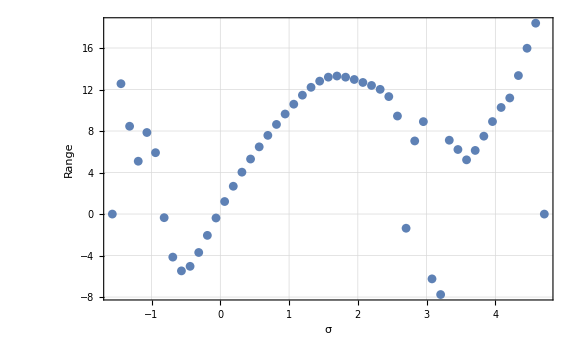

```mathematica
list1={0,π/5,0,newσ,0,0,0,0};
list2={0.45,0.12,1.125,0.44,0.12,1.125,0.01,0.1,.3,0.1,9.81};
σvPairs=Monitor[Table[list1={0,π/5,0,newσ,0,0,0,0};simulateTreb[list1,list2];xt[rg_,ϕg_,θg_]=rg+list2[[4]] Cos[ϕg]-(list2[[6]]/2+list2[[2]]) Cos[θg];ht[θg_,ϕg_]=list2[[1]]-(list2[[3]]/2+list2[[2]]) Sin[θg]-list2[[4]] Sin[ϕg];speed[t_]=(1/9.81)((D[xt[rt[t],ϕt[t],θt[t]],t])^2+(D[ht[θt[t],ϕt[t]],t])^2)Sin[2(θt[t]+Pi/2)];
eq[t_]=Piecewise[{{Tan[ϕt[t]+Pi/2]+Tan[θt[t]+Pi/2],0<t<1},{Undefined,t>1}, {Undefined,t<0}}];
releaseTime=FindRoot[eq[t],{t,0.5}][[All,2]][[1]];
{newσ,speed[releaseTime]},{newσ,-π/2,(3π)/2,π/25}],newσ]//Quiet;
σvPlot1=ListPlot[σvPairs,Frame->True,FrameLabel->{"σ","Range","Range as a Function of Starting Counterweight Angle",""},Axes->Automatic,ImageSize->Large,GridLines->Automatic]
```

In this final section, we explore the effect of the initial counterweight angle on the range of the trebuchet. And lucky for us, this is by far the most interesting graph we’ve come across yet in this study. The first important feature to note is that there is a nice peak right around π/2 that means that we can expect a near optimal performance from the trebuchet when the hanging counterweight starts out just hanging. There are many interesting behaviors to note though, that might not be applicable to the physical model but are still worth noting. First and most importantly, there is a marked upturn at right around 3π/2 where the predicted ranges actually exceed the maximum I labelled at π/2. While this looks promising, there are two problems with it for us, the first being that our trebuchet breaks when we start the counterweight at this angle and the second being that this graph wraps from 3π/2 to -π/2 and the left hand side of the graph doesn’t look very promising. It seems likely that either there is a very sharp maximum which would be very hard to find and replicate in our real model or that there is a lot of variation in this region which would also make it a poor candidate for our real model, which should possess some degree of consistency. The third feature worth noting is the existence of points that clearly break from the trends such as the three around σ = 3. These are likely the result of Mathematica solving for the wrong root when it looks for the release time and that in turn causes a wildly wrong range. As long as a trend is visible in the majority of data points, these outliers are unlikely to have any physical significance.

From Sections 1, 2, and 4, we have found that an optimized parameter set for our trebuchet will likely include a sling length of 0.48 meters, a fulcrum offset of 0.09 meters, and a starting counterweight angle of π/2. I say it will likely include these values because, as we didn’t see in Section 2.1, these values could change with optimization of other parameters such as the counterweight or projectile masses or the throwing arm length. The trebuchet is a complicated enough system to have a huge parameter space and trying to optimize the system’s parameters entirely would require a longer notebook than this.